```mathematica
SetDirectory[NotebookDirectory[]]
fontsize=12;
basestyle={FontFamily->"Latin Modern Roman",FontSize->fontsize};
label[s_]:=Style[s,Italic,fontsize+4]
texify[s_]:=StringReplace[ToString@TeXForm[s],{"\{"->"(","\}"->")"}]
Needs["MaTeX`"];
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{orange}{rgb}{1,0.6,0}"}]
```

/Users/mkoster/Documents/QuatroFile/quarto_Reader_Week_1/figures

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color},\definecolor{orange}{rgb}{1,0.6,0}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

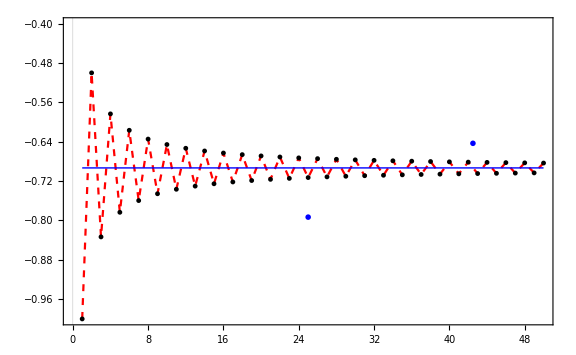

alternating_series.png

```mathematica
nmax=50;
vals=Transpose@{Range[nmax],Accumulate[(-1)^Range[nmax]/Range[nmax]]};


llp=ListLinePlot[vals,PlotRange->{-1,-0.4},Frame->True,FrameLabel->{MaTeX["n",Magnification->1.6],MaTeX["s_n",Magnification->1.6]},PlotTheme->"Scientific",PlotStyle->{Red,Dashed},ImageSize->Large,Epilog->{(*points at partial sums*)Black,PointSize[0.006],Point[vals],(*limit line+labels*)Blue,Thick,Line[{{1,-Log[2]},{nmax,-Log[2]}}],Inset[MaTeX["\\color{blue} -\\ln(2)",Magnification->1.6],{0.85 nmax,0.05-Log[2]}],Inset[MaTeX["s_n=\\sum_{k=1}^n(-1)^k\\frac{1}{{k}}",Magnification->1.6],{0.5 nmax,-0.1-Log[2]}]}]

Export["alternating_series.png",llp,ImageResolution->600]
```

```mathematica
Sum[(-1)^k/k,{k,1,101}]
```

-4915662254209446955930873321941265013941117/7041757898200960193617914702466542659236800

ⅇ^x

ⅇ^a+ⅇ^a (-a+x)

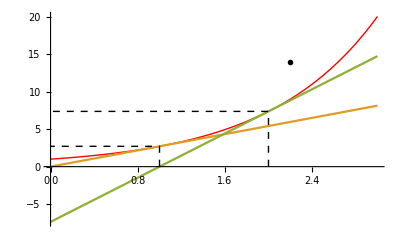

lin_approx_e.png

```mathematica
f[x_]=Exp[x]
g[x_,a_]=f[a]+f'[a](x-a)
Plot[{f[x],g[x,1],g[x,2]},{x,0,3},PlotStyle->{{Red,Thick},,},Epilog->{Inset[MaTeX["\\color{red}f(x)",Magnification->1.4],{2.2,14}],Directive[Black,Dashed],Line[{{1,0},{1,f[1]},{0,f[1]}}],Line[{{2,0},{2,f[2]},{0,f[2]}}]}]
Export["lin_approx_e.png",%,ImageResolution->600]
```

2-ⅇ^(-1+x)

1

2-x

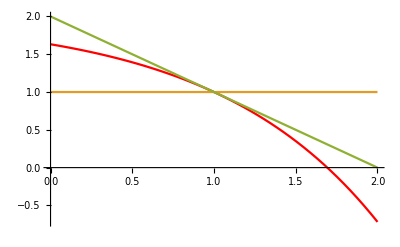

```mathematica
f[x_]=2-Exp[x-1]
g0[x_]=1
g1[x_]=2-x
Plot[{f[x],g0[x],g1[x]},{x,0,2},PlotStyle->{Red,,}]
```

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,FontSize->14];

f[x_]=2-Exp[x-1];
g0[x_]=1;
g1[x_]=2-x;

labs=MaTeX/@{"f(x)=2-e^{x-1}","g_0(x)=1","g_1(x)=2-x"};

Plot[{f[x],g0[x],g1[x]},{x,0,2},PlotStyle->{Red,Automatic,Automatic},AxesLabel->MaTeX/@{"x","y"},PlotLegends->Placed[LineLegend[labs],After],ImageMargins->{{10,60},{10,10}}  (*extra right margin for legend*)]
Export["Taylor_approx.png",%,ImageResolution->600]
```

-Graphics-

Taylor_approx.png

x+1000 x^2

x

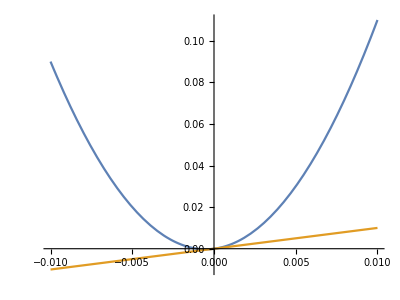

Taylor_bad.png

```mathematica
f[x_]=x+1000 x^2
T1[x_]=x
Plot[{f[x],T1[x]},{x,-0.01,0.01},AspectRatio->3/4,AxesLabel->{MaTeX["\\,\\,x",Magnification->1.5],MaTeX["y",Magnification->1.5]}]
Export["Taylor_bad.png",%,ImageResolution->600]
```

1/x^2

1/Floor[x]^2

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

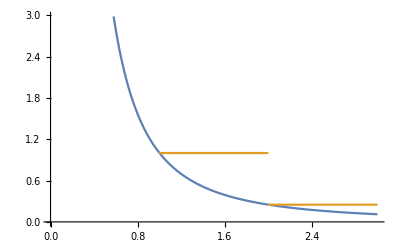

```mathematica
f[x_]=1/x^2
fplus[x_]=f[Floor[x]]
Plot[{f[x],fplus[x]},{x,0,3}]
```

```mathematica
f[x_]:=1/x^2;
fplus[x_]:=f[Ceiling[x]];
vLine[a_?NumericQ,col_:Blue,dashing_:Dashed]:={col,dashing,Line[{{a,0},{a,f[a]}}]}

Needs["MaTeX`"];

f[x_]:=1/x^2;
fplus[x_]:=f[Floor[x]];

Plot[{f[x],fplus[x]},{x,0.5,5.5},PlotStyle->{{Thick,Red},{Dashed,Blue}},Filling->{1->{Axis,Opacity[0.25,Lighter[Red,0.7]]},2->{Axis,Opacity[0.25,Lighter[Blue,0.4]]}},AxesLabel->{MaTeX["x"],MaTeX["y"]},PlotRange->{0,1.2},AspectRatio->3/2,Epilog->{Inset[MaTeX["\\color{red}f(x)=\\frac{1}{x^2}",Magnification->1.4],{3.4,0.6}],vLine@{1,2,3,4}}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-